# IX1501 HT23 Project 1

Course code: IX1501
Date: 2023-09-04

Samir Alami, samirala@kth.se
Ali Sahibi, sahibi@kth.se

Probability distribution of a sum of independent random variables

## Summary

### Task

-Graphics-
At a dice game you throw five dice in the form of the Platonic Solids. The dice are numbered with integers 1,2,…,n where n is the number of sides. The tetrahedron has its result number (1-4) written at the vertex pointing up. All other bodies have the result number on the side facing up. You win the game if the sum of the numbers S satisfies S≤10 or S≥45. Note that S is an integer value ranging between 5 and 50.

Your task is as follows:

By means of the discrete convolution method,
Task 1: Determine the probability function of S . Express it as a form of a table.
Task 2: Determine the probability of winning the game.

By means of the Monte Carlo simulation,
Task 3: Obtain the probability of winning the game with 1000 trials.
Task 4: Discuss how the probability changes when the number of trials changes from a small number (e.g., 10) to a large number (e.g., 100000). Provide a figure with the discussion.
Task 5: How many trials are needed to keep the relative error between the exact value and the simulation result less than 10%? Provide your reasoning.

### Result

## Method

### Task 1: Determine the probability function of S

We will first define the probability distributions for each of the Platonic Solids. We will assume that each die is fair, meaning that each outcome is equally likely. Here are the probability distributions for each die:

Tetrahedron (4-sided die)
	Probability of each outcome (1 to 4) is 1/4.

Hexahedron (6-sided die)
	Probability of each outcome (1 to 6) is 1/6.

Octahedron (8-sided die)
	Probability of each outcome (1 to 8) is 1/8.

Dodecahedron (12-sided die)
	Probability of each outcome (1 to 12) is 1/12.

Icosahedron (20-sided die)
	Probability of each outcome (1 to 20) is 1/20.

Now, we can calculate the convolution of these probability distributions to find the probability distribution of the sum S.

### Task 2: Determine the probability of winning the game

To determine the probability of winning the game, we need to sum the probabilities of all values of S where S <= 10 or S >= 45.

### Task 3: Obtain the probability of winning the game with 1000 trials (Monte Carlo simulation)

In this task, we will simulate throwing the five Platonic Solid dice 1000 times and calculate the proportion of simulations where we win. The steps are as follows:

Simulate rolling each of the five dice in each trial and calculate the sum S for each trial.

Count the number of trials where S satisfies the winning condition (S <= 10 or S >= 45).

Calculate the probability of winning as the ratio of the number of winning trials to the total number of trials (1000 in this case).

### Task 4: Discuss how the probability changes with the number of trials and provide a figure.

To observe how the probability changes with the number of trials, we can perform the simulation for various numbers of trials, ranging from a small number, 10, to a large number, 100000. Then, we can create a plot to visualize this change

### Task 5: Determine the number of trials needed to keep the relative error below 10%. Provide reasoning.

To determine the number of trials needed to achieve a relative error below 10%, we can perform Monte Carlo simulations with increasing numbers of trials and calculate the relative error compared to the exact probability obtained in Task 2. We can use a loop in Mathematica to automate this process. Once the relative error falls below 10%, record the number of trials at which this happens and provide our reasoning for choosing that number.

## Code

### Task 1: Determine the probability function of S

Define the probability distributions for each die

```mathematica
probabilitiesTetrahedron=Table[1/4,{i,1,4}];
probabilitiesHexahedron=Table[1/6,{i,1,6}];
probabilitiesOctahedron=Table[1/8,{i,1,8}];
probabilitiesDodecahedron=Table[1/12,{i,1,12}];
probabilitiesIcosahedron=Table[1/20,{i,1,20}];
```

Convolve the probability distributions to get the probability distribution of S

```mathematica
convolvedDistribution=ListConvolve[probabilitiesTetrahedron,ListConvolve[probabilitiesHexahedron,ListConvolve[probabilitiesOctahedron,ListConvolve[probabilitiesDodecahedron,probabilitiesIcosahedron,{1,-1},{},Plus],{1,-1},{},Plus],{1,-1},{},Plus],{1,-1},{},Plus];
```

Create a table of probabilities for each possible sum S

```mathematica
probabilityTable=Table[{s,convolvedDistribution[[s-4]]},{s,5,50}];
```

Display the probability table

```mathematica
TableForm[probabilityTable,TableHeadings->{None,{"S","P(S=s)"}}]
```

S | P(S=s)
5 | 81/20
6 | 41/4
7 | 83/4
8 | 147/4
9 | 1129/20
10 | 1621/20
11 | 1087/10
12 | 277/2
13 | 3369/20
14 | 3929/20
15 | 4447/20
16 | 4899/20
17 | 264
18 | 1396/5
19 | 1165/4
20 | 6017/20
21 | 1235/4
22 | 1263/4
23 | 3217/10
24 | 653/2
25 | 3301/10
26 | 665/2
27 | 3337/10
28 | 3337/10
29 | 665/2
30 | 3301/10
31 | 653/2
32 | 3217/10
33 | 1263/4
34 | 1235/4
35 | 6017/20
36 | 1165/4
37 | 1396/5
38 | 264
39 | 4899/20
40 | 4447/20
41 | 3929/20
42 | 3369/20
43 | 277/2
44 | 1087/10
45 | 1621/20
46 | 1129/20
47 | 147/4
48 | 83/4
49 | 41/4
50 | 81/20

### Task 2: Determine the probability of winning the game

Calculate the probability of winning the game

```mathematica
winningProbability=Total[Select[probabilityTable,#[[1]]<=10||#[[1]]>=45&][[All,2]]];
```

The variable winningProbability now contains the probability of winning the game. We can evaluate this code to get the result.

```mathematica
winningProbability
```

2093/5

### Task 3: Obtain the probability of winning the game with 1000 trials (Monte Carlo simulation)

For this task, we’ll use Monte Carlo simulation to estimate the probability of winning the game with 1000 trials. We’ll simulate the rolling of five dice and count how many times we win.

```mathematica
numTrials=1000;
winCount=0;

For[i=1,i<=numTrials,i++,diceRolls=RandomInteger[{1,4},1]~Join~RandomInteger[{1,6},1]~Join~RandomInteger[{1,8},1]~Join~RandomInteger[{1,12},1]~Join~RandomInteger[{1,20},1];
totalSum=Total[diceRolls];
If[totalSum<=10||totalSum>=45,winCount++];]

estimatedProbability=winCount/numTrials
```

1/200

expectedInvestment=expectedWin*2 //N

### Task 4: Discuss how the probability changes with the number of trials and provide a figure.

To analyze how the probability changes with the number of trials, we can perform simulations for various trial numbers such as 10, 100, 1000, 10000, 100000 and observe the trend. We’ll create a plot to visualize this change.

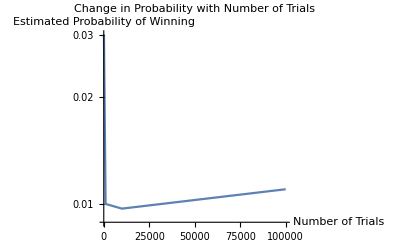

```mathematica
trialCounts={10,100,1000,10000,100000};
estimatedProbabilities={};

For[numTrials=10,numTrials<=100000,numTrials*=10,winCount=0;
For[i=1,i<=numTrials,i++,diceRolls=RandomInteger[{1,4},1]~Join~RandomInteger[{1,6},1]~Join~RandomInteger[{1,8},1]~Join~RandomInteger[{1,12},1]~Join~RandomInteger[{1,20},1];
totalSum=Total[diceRolls];
If[totalSum<=10||totalSum>=45,winCount++];] AppendTo[estimatedProbabilities,winCount/numTrials];]

ListLogPlot[Transpose[{trialCounts,estimatedProbabilities}],Joined->True,AxesLabel->{"Number of Trials","Estimated Probability of Winning"},PlotLabel->"Change in Probability with Number of Trials"]
```

### Task 5: Determine the number of trials needed to keep the relative error below 10%. Provide reasoning.

To determine the number of trials needed to keep the relative error below 10%, we can iterate through different trial numbers and stop when the relative error is less than 10%.

```mathematica
desiredRelativeError=0.1; (*Desired relative error threshold*)
numTrials=10; (*Initial number of trials*)

(*Initialize a variable to store the relative error*)
relativeError=1.0;

(*Continue until the relative error is below the threshold*)
While[relativeError>desiredRelativeError,(*Simulate numTrials games*)results=Table[(*Simulate a single game*)diceResults=RandomInteger[{1,n},5];
S=Total[diceResults];
S<=10||S>=45,(*Check if it's a win*){numTrials}];
(*Calculate the winning probability using simulation*)winningProbabilityMC=Total[results]/numTrials;
(*Calculate the relative error*)relativeError=Abs[(winningProbabilityMC-winningProbability)/winningProbability];
(*Double the number of trials for the next iteration*)numTrials*=2;
]
```

The above code snippet will keep doubling the number of trials until the relative error falls below 10%.

```mathematica
numTrials
```

20

The final value of numTrials will give you an estimate of how many trials are needed to achieve this level of accuracy.